```mathematica
ϵ[n_, kz_]:=w kz + Sign[n] Sqrt[α^2 v^2 kz^2 + Abs[n] α^3 ω^2]
```

```mathematica
ϵ[n, kz]/.{v->1, w->β, α->Sqrt[1-β^2]}
```

kz β+√(kz^2 (1-β^2)+(1-β^2)^(3/2) ω^2 Abs[n]) Sign[n]

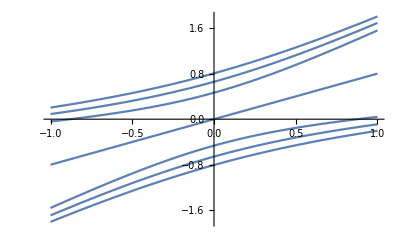

```mathematica
Plot[
Table[
ϵ[n, kz]/.{v->1, w->β, α->Sqrt[1-β^2]}/.{β->0.8, n->n, ω->1},
{n,-3, 3}
],
{kz, -1,1}
]
```

```mathematica
Manipulate[
Plot[
Table[
ϵ[n, kz]/.{v->1, w->β, α->Sqrt[1-β^2]}/.{β->0.8, n->n, ω->1},
{n,-3, 3}
],
{kz, -1,1}
], 
{β, 0, 1.3}
]
```